```mathematica
{Slider[Dynamic[x],{0,1}],Dynamic[x]}
```

{,}

```mathematica
Manipulate[(2x)^2 + 1,{x,0,1}]
```

```mathematica
Manipulate[Plot[(2y)^2 + x, {y, -1, 1}, PlotRange -> {-0.5, 3}],{x,0,1}]
```

Plot::optx: Unknown option Plotrange in Plot[(2\ y)^2 + x, {y, -1, 1}, Plotrange → {-0.5, 3}].

Browse and choose colors: Type Plot[x^2, {x, 0, 1}, PlotStyle -> c], select the c, and click Insert menu -> Color

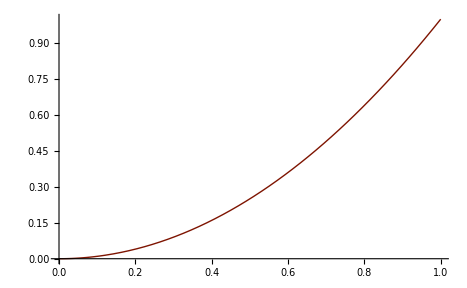
Type -Graphics-

```mathematica
Type Plot[x^2,{x,0,1},PlotStyle->RGBColor[0.494118, 0.0784314, 0.00392157]]
```

Select all elements x for which f[x] is True:

```mathematica
f[x_]:=Mod[x,4]==1&&PrimeQ[x];list=Range[100];Select[list,f]
```

{5,13,17,29,37,41,53,61,73,89,97}

Plot in regions of any shape

```mathematica
Plot3D[Sin[x*y],{x,-2,2},{y,-2,2},RegionFunction->Function[{x,y},1<x^2+y^2<4]]
```

-Graphics3D-

One way to create TraditionalForm input: Type e.g. Integrate[Sin[x], {x, 0, 1}], select it, and press Ctrl+Shift+T

```mathematica
Clear[x]
∫_0^1 sin(x)ⅆx
```

1-Cos[1]

Fill between the 2 curves on a plot:

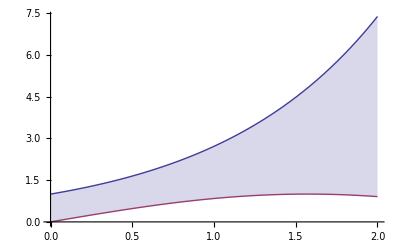

```mathematica
Plot[{Exp[x],Sin[x]},{x,0,2},Filling->{1->{2}}]
```

Plot with custom mesh divisions: http://t.co/B5ACoKyp

```mathematica
Plot3D[x^2 y^3,{x,-3,3},{y,-3,3},MeshFunctions->{#3&},MeshShading->{Yellow,None}]
```

Ctrl+‘ (Mac: Cmd+‘) opens/closes a cell group. Examples: In a Section cell, it closes the section. In an input cell, it hides the output.  Peeter: not clear what this is about (what does open/close mean here?)

Expected smallest value of 3 samples from a normal distribution: . http://j.mp/tXP40D

```mathematica
Mean[OrderDistribution[{NormalDistribution[], 3}, 1]]
```

```mathematica
-3/(2 √π)
{NormalDistribution[], 3}
```

-3/(2 √π)

{NormalDistribution[0,1],3}

```mathematica
{NormalDistribution[0,1], 3}
```

{NormalDistribution[0,1],3}

```mathematica
Ten uniformly random numbers:
RandomReal[{0,1},10]

.Ten Poisson-distributed random integers:.
```

random Ten uniformly (numbers:{0.507041,0.280988,0.775148,0.736174,0.160687,0.852864,0.725465,0.67298,0.434337,0.789943})

```mathematica
RandomVariate[PoissonDistribution[3],10]
```

{2,1,3,3,2,1,6,6,3,4}

```mathematica
5 dimensional array:.Transpose the 2nd and 5th dimensions:.http://j.mp/uiVogc
```

```mathematica
a=RandomReal[1,{2,2,2,2,2}]
```

{{{{{0.396869,0.51937},{0.937078,0.385916}},{{0.527994,0.631125},{0.726873,0.77271}}},{{{0.232632,0.944449},{0.564201,0.381406}},{{0.687484,0.98167},{0.134408,0.0488917}}}},{{{{0.810251,0.114103},{0.796241,0.22085}},{{0.723424,0.554443},{0.340736,0.634164}}},{{{0.419572,0.0164011},{0.777796,0.89226}},{{0.524723,0.363034},{0.275438,0.540564}}}}}

```mathematica
Transpose[a,{1,5,3,4,2}]
```

{{{{{0.396869,0.232632},{0.937078,0.564201}},{{0.527994,0.687484},{0.726873,0.134408}}},{{{0.51937,0.944449},{0.385916,0.381406}},{{0.631125,0.98167},{0.77271,0.0488917}}}},{{{{0.810251,0.419572},{0.796241,0.777796}},{{0.723424,0.524723},{0.340736,0.275438}}},{{{0.114103,0.0164011},{0.22085,0.89226}},{{0.554443,0.363034},{0.634164,0.540564}}}}}

```mathematica
MathematicaTip:Fit model parameters to data:.http://t.co/bmqk4ZSC
```

```mathematica
Clear[x, a, b]
NonlinearModelFit[{{0,1},{1,0},{3,2},{5,4},{6,4},{7,5}},Log[a+b*x^2],{a,b},x]
```

FittedModel[Log[1.50632+1.42633 x^2]]

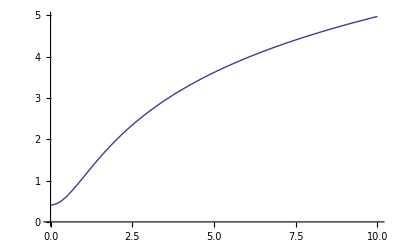

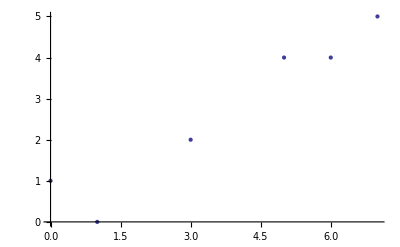

```mathematica
Plot[ Log[1.5063204891556878+1.4263297975161129 x^2], {x, 0, 10}]
Clear[t]
t := {{0,1},{1,0},{3,2},{5,4},{6,4},{7,5}}
ListPlot[t]
```